# LEP Bound on Scalar

```mathematica
Quit[]
```

## SM Parameters

```mathematica
mb=4.19;
mc=1.27;
mτ=1.78;
```

## Branching Ratio

```mathematica
bBR[mS_]:=(mb^2 Max[(mS^2-4 mb^2)^3,0])/(mb^2 Max[(mS^2-4 mb^2)^3,0]+mc^2 Max[(mS^2-4 mc^2)^3,0]+mτ^2 Max[(mS^2-4 mτ^2)^3,0]);
cBR[mS_]:=(mc^2 Max[(mS^2-4 mc^2)^3,0])/(mb^2 Max[(mS^2-4 mb^2)^3,0]+mc^2 Max[(mS^2-4 mc^2)^3,0]+mτ^2 Max[(mS^2-4 mτ^2)^3,0]);τBR[mS_]:=(mτ^2 Max[(mS^2-4 mτ^2)^3,0])/(mb^2 Max[(mS^2-4 mb^2)^3,0]+mc^2 Max[(mS^2-4 mc^2)^3,0]+mτ^2 Max[(mS^2-4 mτ^2)^3,0]);
```

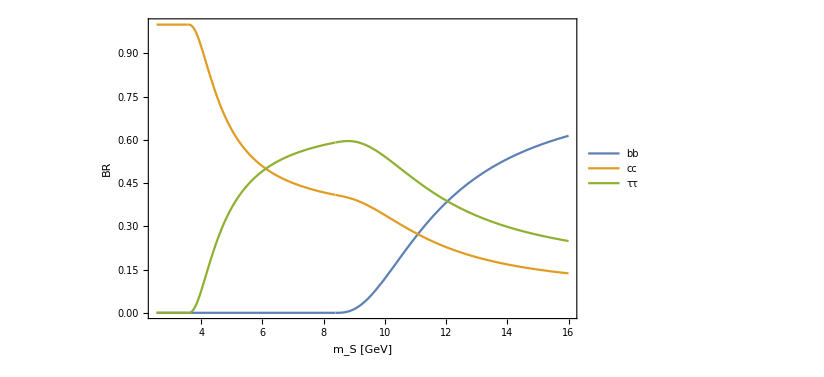

```mathematica
Plot[{bBR[mS],cBR[mS],τBR[mS]},{mS,2mc,16},PlotLegends->Placed[LineLegend[{Style["bb",FontFamily->"Times",FontSize->16],Style["cc",FontFamily->"Times",FontSize->16],Style["ττ",FontFamily->"Times",FontSize->16]},Spacings->0.1,LegendMarkerSize->30,LegendFunction->(Framed[#1, FrameMargins -> 0,RoundingRadius->5] & )],{0.9,0.8}],BaseStyle->{FontSize->20,FontFamily->"Times"},Frame->True,FrameLabel->{Style["m_S [GeV]",FontFamily->"Times",FontSize->20],Style["BR",FontFamily->"Times",FontSize->20]},LabelStyle->{Black},FrameTicksStyle->{Directive[FontFamily->"Times",FontSize->20]}]
```

## LEP bound

```mathematica
bb‵limit[mS_]:=Interpolation[Import[NotebookDirectory[]<>"bb.csv"]][mS];
ττ‵limit[mS_]:=Interpolation[Import[NotebookDirectory[]<>"tautau.csv"]][mS];
independent‵limit[mS_]:=Interpolation[Import[NotebookDirectory[]<>"independent.csv"]][mS];
```

```mathematica
bb‵bound[mS_/;mS≥12.4]=√((bb‵limit[mS])/bBR[mS]);
bb‵bound[mS_/;mS<12.4]=1;
ττ‵bound[mS_/;mS≥3.9]=√((ττ‵limit[mS])/τBR[mS]);
ττ‵bound[mS_/;mS<3.9]=1;
```

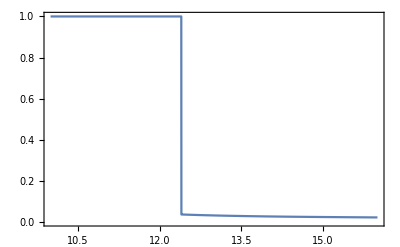

```mathematica
Plot[bb‵bound[mS],{mS,10,16}]
```

```mathematica
bb‵bound[10]
```

1

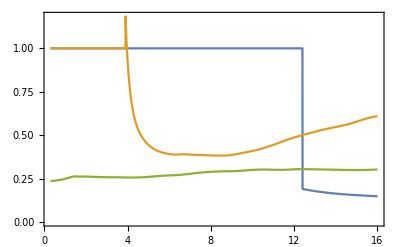

```mathematica
Plot[{bb‵bound[mS],ττ‵bound[mS],√(independent‵limit[mS])},{mS,0.3,16}]
```

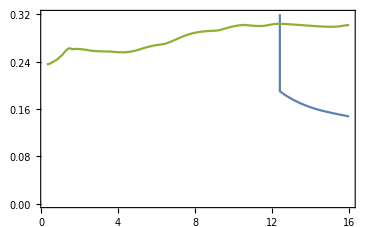

```mathematica
Plot[{bb‵bound[mS],ττ‵bound[mS],√(independent‵limit[mS])},{mS,0.3,16},PlotRange->{{0.3,16},{0,0.32}}]
```

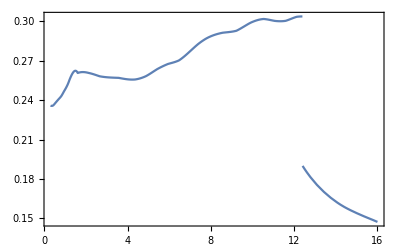

```mathematica
Plot[Min[bb‵bound[mS],ττ‵bound[mS],√(independent‵limit[mS])],{mS,0.3,16}]
```

```mathematica
boundlist=Table[{mS,Min[bb‵bound[mS],ττ‵bound[mS],√(independent‵limit[mS])]},{mS,0.3,16.,0.1}];
```

InterpolatingFunction::dmval: Input value {3.9} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
Export[ParentDirectory[NotebookDirectory[]]<>"/output/LEPbound.csv",boundlist];
```

```mathematica
boundfunc[mS_]:=Interpolation[boundlist][mS]
```

```mathematica
boundlist
```

{{0.3,0.235899},{0.4,0.235819},{0.5,0.237274},{0.6,0.239179},{0.7,0.240978},{0.8,0.242789},{0.9,0.245383},{1.,0.248178},{1.1,0.251164},{1.2,0.255024},{1.3,0.258755},{1.4,0.261434},{1.5,0.262397},{1.6,0.260889},{1.7,0.261153},{1.8,0.261376},{1.9,0.261377},{2.,0.261195},{2.1,0.26087},{2.2,0.260494},{2.3,0.260063},{2.4,0.259575},{2.5,0.259051},{2.6,0.258512},{2.7,0.258083},{2.8,0.257832},{2.9,0.25763},{3.,0.257469},{3.1,0.257342},{3.2,0.257242},{3.3,0.257163},{3.4,0.257098},{3.5,0.257039},{3.6,0.256922},{3.7,0.256621},{3.8,0.256339},{3.9,0.256091},{4.,0.255891},{4.1,0.255751},{4.2,0.255685},{4.3,0.255709},{4.4,0.255866},{4.5,0.256185},{4.6,0.256603},{4.7,0.257118},{4.8,0.25773},{4.9,0.258449},{5.,0.259368},{5.1,0.260352},{5.2,0.261374},{5.3,0.262407},{5.4,0.263424},{5.5,0.264305},{5.6,0.265124},{5.7,0.265897},{5.8,0.266624},{5.9,0.267306},{6.,0.267839},{6.1,0.268275},{6.2,0.268725},{6.3,0.269227},{6.4,0.269819},{6.5,0.27063},{6.6,0.271772},{6.7,0.273028},{6.8,0.274372},{6.9,0.275778},{7.,0.277221},{7.1,0.278681},{7.2,0.280126},{7.3,0.281531},{7.4,0.282865},{7.5,0.284064},{7.6,0.285177},{7.7,0.286204},{7.8,0.287135},{7.9,0.287936},{8.,0.288647},{8.1,0.289276},{8.2,0.289829},{8.3,0.290315},{8.4,0.290739},{8.5,0.291111},{8.6,0.291397},{8.7,0.291568},{8.8,0.291732},{8.9,0.29191},{9.,0.292122},{9.1,0.292391},{9.2,0.292736},{9.3,0.293426},{9.4,0.294287},{9.5,0.295204},{9.6,0.29615},{9.7,0.297101},{9.8,0.29803},{9.9,0.298892},{10.,0.299595},{10.1,0.300219},{10.2,0.300755},{10.3,0.301196},{10.4,0.30153},{10.5,0.301749},{10.6,0.301706},{10.7,0.301476},{10.8,0.301185},{10.9,0.300864},{11.,0.300545},{11.1,0.300293},{11.2,0.30016},{11.3,0.300096},{11.4,0.30011},{11.5,0.300214},{11.6,0.300438},{11.7,0.300979},{11.8,0.301582},{11.9,0.302206},{12.,0.30281},{12.1,0.303353},{12.2,0.303596},{12.3,0.303699},{12.4,0.190143},{12.5,0.18768},{12.6,0.185355},{12.7,0.183157},{12.8,0.181077},{12.9,0.179107},{13.,0.177237},{13.1,0.175463},{13.2,0.173777},{13.3,0.172173},{13.4,0.170647},{13.5,0.169193},{13.6,0.167809},{13.7,0.166489},{13.8,0.165231},{13.9,0.164032},{14.,0.162888},{14.1,0.161797},{14.2,0.160757},{14.3,0.159766},{14.4,0.158843},{14.5,0.157973},{14.6,0.157139},{14.7,0.156338},{14.8,0.155566},{14.9,0.15482},{15.,0.154097},{15.1,0.153393},{15.2,0.152694},{15.3,0.152008},{15.4,0.151337},{15.5,0.150677},{15.6,0.150029},{15.7,0.149391},{15.8,0.148747},{15.9,0.148065},{16.,0.147407}}